```mathematica
europes=CountryData["Europe"]
```

{Albania,Andorra,Austria,Belarus,Belgium,Bosnia and Herzegovina,Bulgaria,Croatia,Cyprus,Czech Republic,Denmark,Estonia,Faroe Islands,Finland,France,Germany,Gibraltar,Greece,Guernsey,Hungary,Iceland,Ireland,Isle of Man,Italy,Jersey,Kosovo,Latvia,Liechtenstein,Lithuania,Luxembourg,Macedonia,Malta,Moldova,Monaco,Montenegro,Netherlands,Norway,Poland,Portugal,Romania,San Marino,Serbia,Slovakia,Slovenia,Spain,Svalbard,Sweden,Switzerland,Ukraine,United Kingdom,Vatican City}

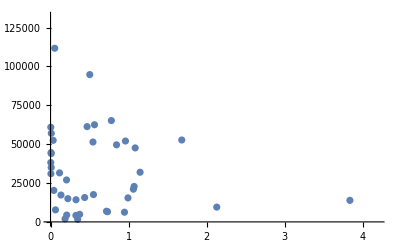

```mathematica
europesPopGDP = Map[Block[{tmp = #},Map[CountryData[tmp,#]&,{"Population","GDPPerCapita"}]]&,europes] ;
ListPlot[europesPopGDP]
```